# SPAC Model (from roots to leaves)

## Simple code for the Soil-Plant-Atmosphere Continuum Model Based on Eco-hydrology by Rodriguez-Iturbe and Porporato & Daly et al., 2004a,b. Author: Annalisa Molini Last Updated: October 23, 2024

```mathematica
(*General Settings*)
ClearAll;
SetOptions[Plot,BaseStyle->FontSize->14]; (*Set Font at 14pt*)
Clear[callout]
callout[point_,label_,markerSize_:2]:=Inset[ListPlot[{Callout[{0,0},label]},ImageSize->All,Axes->False,AlignmentPoint->{0,0},PlotStyle->AbsolutePointSize[markerSize]]/. _Point->Nothing,point]
```

```mathematica
(*General Constants*)
ρw=998; (*[kg/m^3], Water density *)
νw=18/1000/ρw; (* [m^3/mol], Molecular volume of liquid water *)
R = 8.314; (*[J/(mol K)], Universal Gas Constant*)
g= 9.8; (*[m/s^2], Gravitational acceleration*)
λw=2.5*10^6;(* λw=2.501 10^6-2370 Ta, [J/kg], Latent heat of water vaporization (it actually depends on Ta as well) (not used?)*)
cp = 1012; (*[J/(kg K)], Specific Heat of Air at constant pressure*)
ρ = 1.23; (*[kg/m^3], Air Density (at standard pressure and temperature)*)
```

```mathematica
(*Plant Constants, for Eastern decidous forest*)
(*hc=20 ;(*[m], Canopy height, assummed height of eastern decidous forest *)
LAI =5.2; (*[dimensionless], Leaf area per unit ground area*)
RAIW= 9.8; (*[dimensionless], Root Area Index under well watered conditions, value for a decidous forest*)
Zr =.4;(*[m], Rooting depth, assume decidous forest*)*)

hc=20 ;(*[m], Canopy height, assummed height of eastern decidous forest *)
LAI =1.4; (*[dimensionless], Leaf area per unit ground area*)
RAIW= 5; (*[dimensionless], Root Area Index under well watered conditions, value for a decidous forest*)
Zr =.6;(*[m], Rooting depth, assume decidous forest*)
```

```mathematica
(*The Soil Compartment:
Parametrizations for a LOAMY SAND(This can adapted to different kinds of soils using Table 3.1 in Porporato and Yin)*)
(*Soil Water Retention Curve*)
Ψss=-1.43*10^-3;(*[MPa], Air entry suction*)
b=5.39;(*[Unitless], Parameter water retention curve related to soil pore-size distribution*)
Ks=20 (*[cm/day], Saturated Hydraulic Conductivity*)
c=2+2.5*b;(*[Unitless], Exponenet of the hydraulic conductivity curve*)
n=.45; (*[%], Porosity (not used?)*)  
sh=.19; (*[%], Hydroscopic soil moisture (not used?) *)
sw=0.24 ;(*[%], Wilting soil moisture*)
sstar=0.57 ;(*[%], Incipient stomata closure soil moisture*)
sfc=0.65 ;(*[%], Field capacity soil moisture*)

(* Soil to root conductance *)
a= 8; (*Parameter accounting for root growth*)
RAI[s_]:=RAIW* s^-a;
p1=Plot[RAI[s],{s,sfc,1},PlotStyle->{Red,Thickness[0.01]},PlotRange->{{sw,1},{0,RAIW*sstar^-a}}];
p2=Plot[RAI[s],{s,sstar,sfc},PlotStyle->{Black,Dashed,Thickness[0.005]},PlotRange->{{sw,1},{0,RAIW*sstar^-a}}];
g1=Graphics[{Point[{{sfc,1}}],callout[{sfc,1},"",1]}];
g2=Graphics[{Point[{{sstar,1}}],callout[{sstar,1},"",1]}];
g3=Graphics[{Point[{{sw,1}}],callout[{sw,1},"",1]}];

Show[p1,p2,g1,g2,g3,Frame->True,Epilog->{Black,Dashed,Line[{{sstar,0},{sstar,RAIW*sstar^-a}}],Line[{{sfc,0},{sfc,RAIW*sfc^-a}}]},PlotLabel->"RAI as a function of relative soil moisture, s",AspectRatio->1,FrameLabel-> {"",""},LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460]
```

20

-Graphics-
-Graphics-

0.00848528

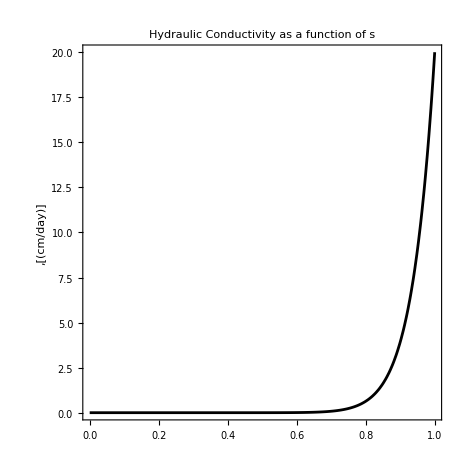

```mathematica
dr= .6*10^-3; (*[m],
Average root diameter*)
(*lambda[s_]:=Sqrt[dr*Zr/RAI[s]] *)
lambda=Sqrt[dr*Zr/RAIW](*[m],
Typical distance traveled from the soil to the surface of the roots*)
K[s_]:=Ks*s^c(* [cm/day], Hydraulic conductivity as a function of soil moisture, s*)
KsPlot=Plot[K[s],{s,0,1},Frame->True,AspectRatio->1,FrameLabel-> {"",",[(cm/day)]"},PlotStyle->Black,PlotRange->{{0,1},{0,Ks}},PlotRangeClipping->True, PlotLabel->"Hydraulic Conductivity as a function of s",LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460]
```

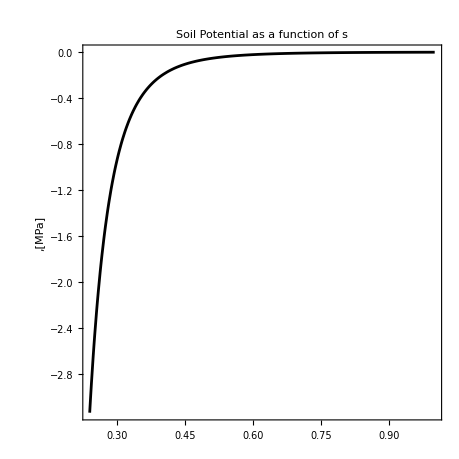

```mathematica
(*Soil Potential and Water retention curve*)
ψs[s_]:=Ψss*s^-b  (*[MPa], Soil Potential*)
PsisPlot=Plot[ψs[s],{s,sw,1},Frame->True,AspectRatio->1,FrameLabel-> {"",",[MPa]"},PlotStyle->Black,
PlotRange->{{sw,1},{0,Ψss*sw^-b}},
PlotRangeClipping->True, PlotLabel->"Soil Potential as a function of s",LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460]
```

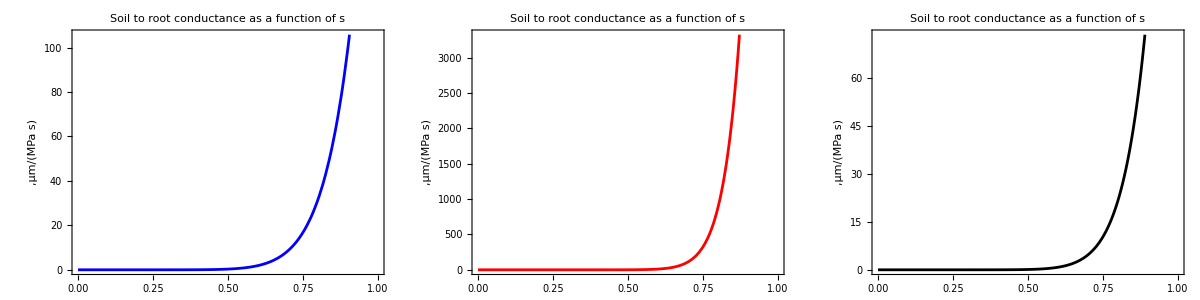

```mathematica
gsr2[s_]:= K[s]/(g*ρw*lambda)*10^10/60/60/24(*[μm/(MPa s)] Soil to Root Conductance*)
L[s_]:=.11574 Ks s^(2 b +3)(*μm/s, Leakage losses*)                                   
gsr3[s_]:= (K[s]*√RAI[s])/(π g ρw Zr)*10^10/60/60/24(*[μm/(MPa s)] Soil to Root Conductance 2*)

L[s_]:=.11574 Ks s^(2 b +3)(*μm/s, Leakage losses*)                                   
gsr[s_]:= (L[s]*√RAI[s]*10^6)/(π g ρw Zr)(*[μm/(MPa s)] *)
Ksat=K[1];
lamsat=lambda[1];
gsrPlot=Plot[gsr[s],{s,0,1},Frame->True,AspectRatio->1,FrameLabel-> {"",",μm/(MPa s)"},PlotStyle->Blue,
PlotRangeClipping->True, PlotLabel->"Soil to root conductance as a function of s",LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460];
gsrPlot2=Plot[gsr2[s],{s,0,1},Frame->True,AspectRatio->1,FrameLabel-> {"",",μm/(MPa s)"},PlotStyle->Red,
PlotRangeClipping->True, PlotLabel->"Soil to root conductance as a function of s",LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460];
gsrPlot3=Plot[gsr3[s],{s,0,1},Frame->True,AspectRatio->1,FrameLabel-> {"",",μm/(MPa s)"},PlotStyle->Black,
PlotRangeClipping->True, PlotLabel->"Soil to root conductance as a function of s",LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460];
Grid[{{gsrPlot,gsrPlot2,gsrPlot3}}]
```

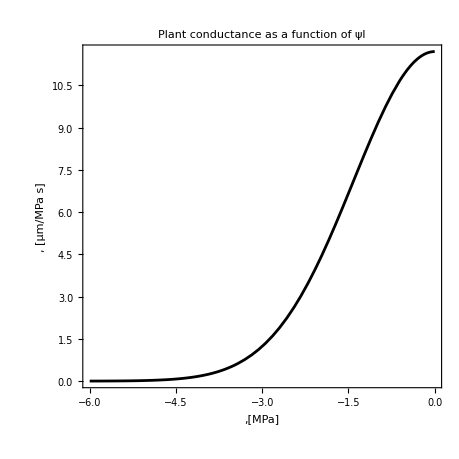

```mathematica
(*The Plant Compartment: *)
(*Vulnerability Curve, following Sperry et al., 2002; Kastul et al., 2003*)
cvc= 2; (*
Parameter of Vulnerability Curve, 1*)
dvc=2 ;(*[MPa], 
Parameter of Vulnerability Curve, 2*)
gpmax = 11.7; (*[μm/(MPa s)], 
Maximum Plant Conductance for Vulnerability curve*)
gp[ψl_]:=gpmax * E^(-(-ψl/dvc)^cvc) ;(*[μm/(MPa s)],Plant Conductance*)
gpPlot=Plot[gp[ψl],{ψl,-6,0},Frame->True,AspectRatio->1,FrameLabel-> {",[MPa]",", [μm/MPa s]"},PlotStyle->Black,
PlotRangeClipping->True, PlotLabel->"Plant conductance as a function of ψl",LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460]
```

```mathematica
(*Soil-Root-Plant Conductance*)
gsrp[ψl_,s_]:=(LAI*gp[ψl]*gsr[s])/(gsr[s]+LAI*gp[ψl]);(*[μm/(MPa s)], Soil-Root-Plant Conductance *)
plg1=Plot[gsrp[ψl,s]/.{s->.5},{ψl,-6,0},Frame->True,AspectRatio->1,FrameLabel-> {",[MPa]",", [μm/MPa s]"},PlotStyle->Black,
PlotRangeClipping->True, PlotLabel->" as a function of ψl",PlotLabels->{""},LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460]
(*plg2=Plot[gsrp[ψl,s]/.{s->sstar},{ψl,-6,0},Frame->True,AspectRatio->1,FrameLabel-> {",[MPa]",", [μm/MPa s]"},PlotStyle->Black,
PlotRangeClipping->True, PlotLabel->" as a function of ψl",PlotLabels->{""},LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460];
plg3=Plot[gsrp[ψl,s]/.{s->sw},{ψl,-6,0},Frame->True,AspectRatio->1,FrameLabel-> {",[MPa]",", [μm/MPa s]"},PlotStyle->Black,
PlotRangeClipping->True, PlotLabel->" as a function of ψl",PlotLabels->{""},LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460];
Show[plg1,plg2,plg3,PlotRange->{{-6,0},{0,1.8}}]*)
```

-Graphics-

```mathematica
Plot[Evaluate@Table[gsrp[ψl,s],{s,{sw,sstar,sfc}}],{ψl,-6,0},Frame->True,AspectRatio->1, PlotRange->{{-6,0},{0,3.5}},FrameLabel-> {",[MPa]",", [μm/MPa s]"},PlotStyle->ColorData[10,"ColorList"],PlotRangeClipping->True,PlotLabels->{"","",""},LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460]
```

-Graphics-

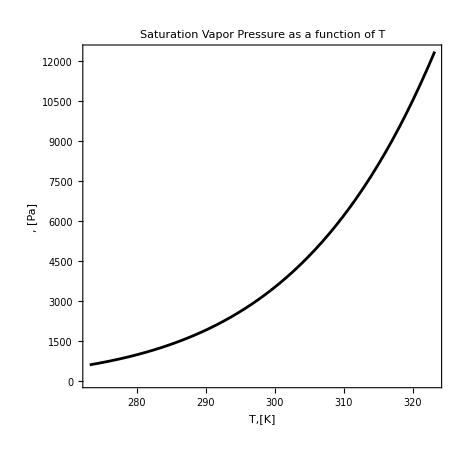

```mathematica
(*The Atmosphere Compartment: *)
p0 = 101.325 10^3; (*Pa, Atmospheric pressure*)
Ra = 287; (*[J/(kg K)], Specific Gas Constant for Air*)
esat[Ta_]:=610.94*Exp[(17.625*(Ta-273.15))/((Ta-273.15)+243.04)];(*[Pa], Saturated vapor pressure from the August–Roche–Magnus Formula [T is in K all across the notebook]]*)
gpPlot=Plot[esat[Ta],{Ta,0+273.15,50+273.15},Frame->True,AspectRatio->1,FrameLabel-> {"T,[K]",", [Pa]"},PlotStyle->Black,
PlotRangeClipping->True, PlotLabel->"Saturation Vapor Pressure as a function of T",LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460]
```

```mathematica
ea[Ta_,RH_]:=RH/100*esat[Ta]; (*[Pa], Atm. vapor pressure*)
Plot[Evaluate@Table[ea[Ta,RH],{RH,{20,30,50,80,100}}],{Ta,0+273.15,40+273.15},Frame->True,AspectRatio->1, FrameLabel-> {",[K]",", [Pa]"},PlotStyle->ColorData[10,"ColorList"],PlotRangeClipping->True,PlotLabels->{"=20%","=30%","=50%","=80%","Saturation"},LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460]
```

-Graphics-

```mathematica
VPD[Ta_,RH_]:=esat[Ta]-ea[Ta,RH]; (*[Pa], Vapor Pressure Deficit*)
vpd1=Plot[Evaluate@Table[VPD[Ta,RH],{Ta,{15+273.15,25+273.15,40+273.15}}],{RH,20,100},Frame->True,AspectRatio->1, FrameLabel-> {",[%]","VPD, [Pa]"},PlotStyle->ColorData[10,"ColorList"],PlotRangeClipping->True,PlotLabels->{"=15 C","=25 C","=40 C"},LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460];
vpd2=Plot[Evaluate@Table[VPD[Ta,RH],{RH,{20,30,50,100}}],{Ta,15+273.15,40+273.15},Frame->True,AspectRatio->1, FrameLabel-> {",[K]","VPD, [Pa]"},PlotStyle->ColorData[10,"ColorList"],PlotRangeClipping->True,PlotLabels->{"=20%","=30%","=50%","=100%"},LabelStyle->{FontFamily->"Helvetica",Black},ImageSize->460];

Grid[{{vpd1,vpd2}}]
```

-Graphics-

```mathematica
el[ψl_,Tl_,hc_]:=esat[Tl]*Exp[(νw*(ψl-g*ρw*hc))/(R*Tl)] (*[MPa], Leaf Vapor Pressure *)
```

```mathematica
(*Modeling Stomatal Conductance with Jarvis' (Empirical) Approach *)
 
(*Constants for Stomatal Conductance (gs) Jarvis empirical equations from Daly et al. 2004a*)
k1=.005; (*[m^2/W], From Jones 1992, p. 156, 
Effect of increasing illumination on gs*)
k2 = .0016 ;(*[K^-2], Lhomme et al. 1996,
Effect of temperature on gs*)
gb = 20; (*[mm/s] Leaf Boundary Area Conductance (unit leaf area)*)
Topt = 298; (*[K], Lhomme et al. 1996*)
ψl1=-.05 ;(* [MPa] from Daly et al. for a C3 plant in semiarid climate*)
ψl0= -4.5; (* [MPa] for a C3 plant in a semiarid climate*)
Dx =1250; (*Pa from Daly et al. 2004*) 
gsmax =25; (*[mm/s] from Daly et al. maximum stomatal conductance*)
```

```mathematica
(*gs(Javis), stomatal conductance, function:*)
fϕ[ϕ_]:=1-E^(-k1*ϕ) (* Light Limitation*)
fTa[Ta_]:=1-k2*(Ta - Topt)^2 (* Temperature Limitation*)
fψl[ψl_]:=Piecewise[{{0, ψl< ψl0},{(ψl-ψl0)/(ψl1-ψl0),ψl0  ≤ ψl≤ψl1},{1,ψl>ψl1}}] (*Water Limitation with ψl in MPa*)
fD[Ta_,RH_]:=1/(1+VPD[Ta,RH]/Dx)(*Air Humidity Limitation*)
gs[ϕ_,Ta_,ψl_,RH_]:=gsmax*fϕ[ϕ]*fTa[Ta]*fψl[ψl]*fD[Ta,RH](*[mm/s], Jarvis' Stomatal Conductance*)
gs[400,303,-1,40]
```

5.41149

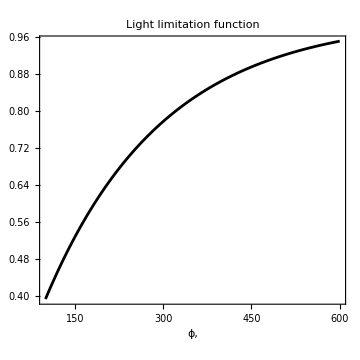
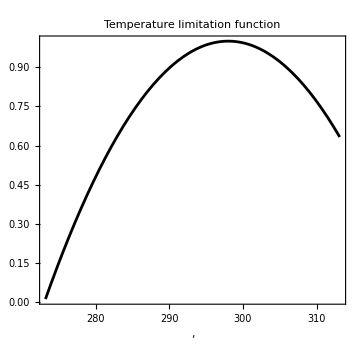
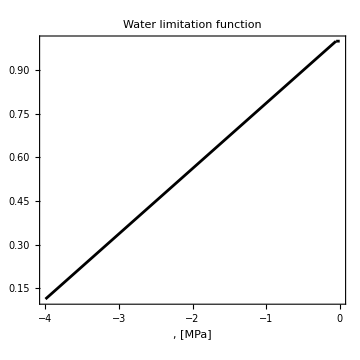
-Graphics- | -Graphics-
-Graphics- |

```mathematica
plotlight=Plot[fϕ[ϕ],{ϕ,100,600},PlotRange->All,Frame->True,AspectRatio->1,FrameLabel-> {"ϕ, ",""},PlotStyle->Black,
PlotRangeClipping->True, ImageSize->360,LabelStyle->{FontFamily->"Helvetica",Black},PlotLabel->"Light limitation function"];
plotTopt=Plot[fTa[Ta],{Ta,0+273.15,40+273.15},PlotRange->All,Frame->True,AspectRatio->1,FrameLabel-> {", ",""},PlotStyle->Black,
PlotRangeClipping->True, ImageSize->360,LabelStyle->{FontFamily->"Helvetica",Black},PlotLabel->"Temperature limitation function"];
plotPsil=Plot[fψl[ψl],{ψl,-4,0},PlotRange->All,Frame->True,AspectRatio->1,FrameLabel-> {", [MPa]",""},PlotStyle->Black,
PlotRangeClipping->True, ImageSize->360,LabelStyle->{FontFamily->"Helvetica",Black},PlotLabel->"Water limitation function"];
Grid[{{plotlight,plotTopt},{plotPsil}}]
```

```mathematica
(*Constants for atmospheric conductance equation*)
k =.41; (*Von Karman Constant*)
d = .7*hc;(*m, percentage of canopy height*) 
z0=d/10; (*m, approximately*)
z0q=.2*z0 ; (*m, approximately*)
uw= 5; (*[m/s], Wind Speed*)
```

```mathematica
(*ga, atmospheric conductance *)
ga=(100*uw* k^2)/(Log[(hc-d)/z0]Log[(hc-d)/z0q])(*mm/s*)
```

18.8451

```mathematica
(* given atm. variables for assigned Tleaf *)
Ta=20+273.15;(* Kelvin, Atm. temp *)
RH=30 ;(* %, Rel. Humidity *)
ϕ=400; (* [W/m^2], leaf available energy *)
gs[ϕ_,Ta_,ψl_,RH_]:=gsmax*fϕ[ϕ]*fTa[Ta]*fψl[ψl]*fD[Ta,RH](*[mm/s], Jarvis' Stomatal Conductance*)
```

```mathematica
(*Conductance from the stomata to the atmosphere*)
gsa[ϕ_,Ta_,ψl_,RH_]:=(ga*gs[ϕ,Ta,ψl,RH])/(ga+gs[ϕ,Ta,ψl,RH])(*mm/s*)
```

```mathematica
esat[Ta_]:=610.94*Exp[(17.625*(Ta-273.15))/((Ta-273.15)+243.04)];(*[Pa], Saturated vapor pressure from the August–Roche–Magnus Formula [T is in K all across the notebook]]*)
ea[Ta_,RH_]:=RH/100*esat[Ta]; (*[Pa], Atm. vapor pressure*)
el[Tl_,ψl_,hc_]:=esat[Tl]*Exp[(νw*(ψl-g*ρw*hc))/(R*Tl)] (*[Pa], Leaf Vapor Pressure *)


ET1[ψl_,s_]:=gsrp[ψl,s](ψs[s]-ψl)*10^-3*60*60*24(*[mm/day], Plant water balance*)
ET2[ϕ_,Ta_,ψl_,RH_,Tl_,hc_]:=ρ/ρw*gsa[ϕ,Ta,ψl,RH]*0.622/p0*(el[Tl,ψl,hc]-ea[Ta,RH])*60*60*24; (*, [mm/day]leaf water balance*)
```

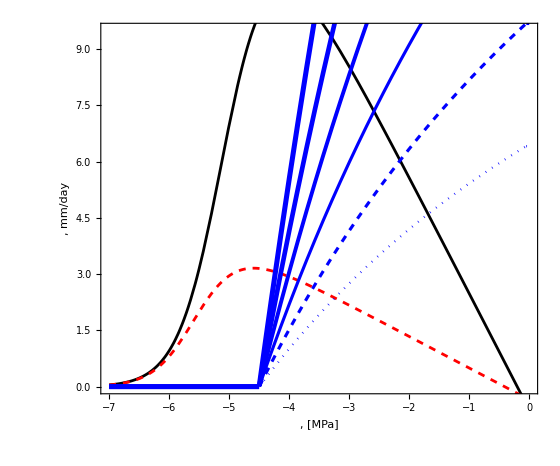

```mathematica
s1=Plot[ET1[ψl,0.4],{ψl,-7,0},PlotStyle->Black,PlotLabels->Placed[{""},{Above,Right}]];
s11=Plot[ET1[ψl,0.35],{ψl,-7,0},PlotStyle->{Red,Dashed},PlotLabels->Placed[{""},{Above,Right}]];
s2=Plot[ET2[ϕ,Ta,ψl,RH,293,20],{ψl,-7,0},PlotStyle->{Blue,Thickness[0.003],Dotted},PlotLabels->Placed[{""},{Above,Right}],PlotRange->{{-7,0},{0,12}}];
s3=Plot[ET2[ϕ,Ta,ψl,RH,298,20],{ψl,-7,0},PlotStyle->{Blue,Thickness[0.004],Dashed},PlotLabels->Placed[{""},{Above,Right}],PlotRange->{{-7,0},{0,12}}];
s4=Plot[ET2[ϕ,Ta,ψl,RH,303,20],{ψl,-7,0},PlotStyle->{Blue,Thickness[0.004]},PlotLabels->Placed[{""},{Above,Left}],PlotRange->{{-7,0},{0,12}}];
s5=Plot[ET2[ϕ,Ta,ψl,RH,308,20],{ψl,-7,0},PlotStyle->{Blue,Thickness[0.005]},PlotLabels->Placed[{""},{Above,Left}],PlotRange->{{-7,0},{0,12}}];
s6=Plot[ET2[ϕ,Ta,ψl,RH,313,20],{ψl,-7,0},PlotStyle->{Blue,Thickness[0.006]},PlotLabels->Placed[{""},{Above,Left}],PlotRange->{{-7,0},{0,12}}];
s7=Plot[ET2[ϕ,Ta,ψl,RH,318,20],{ψl,-7,0},PlotStyle->{Blue,Thickness[0.0065]},PlotLabels->Placed[{""},{Above,Right}],PlotRange->{{-7,0},{0,12}}];
Show[s1,s11,s2,s3,s4,s5,s6,s7,Frame->True,AspectRatio->1/1.2,FrameLabel-> {", [MPa]",", mm/day"}, ImageSize->560,LabelStyle->{FontFamily->"Helvetica",Black},PlotRange->{{-7,0},{0,9.5}}] (**)
```